{2,1+v}

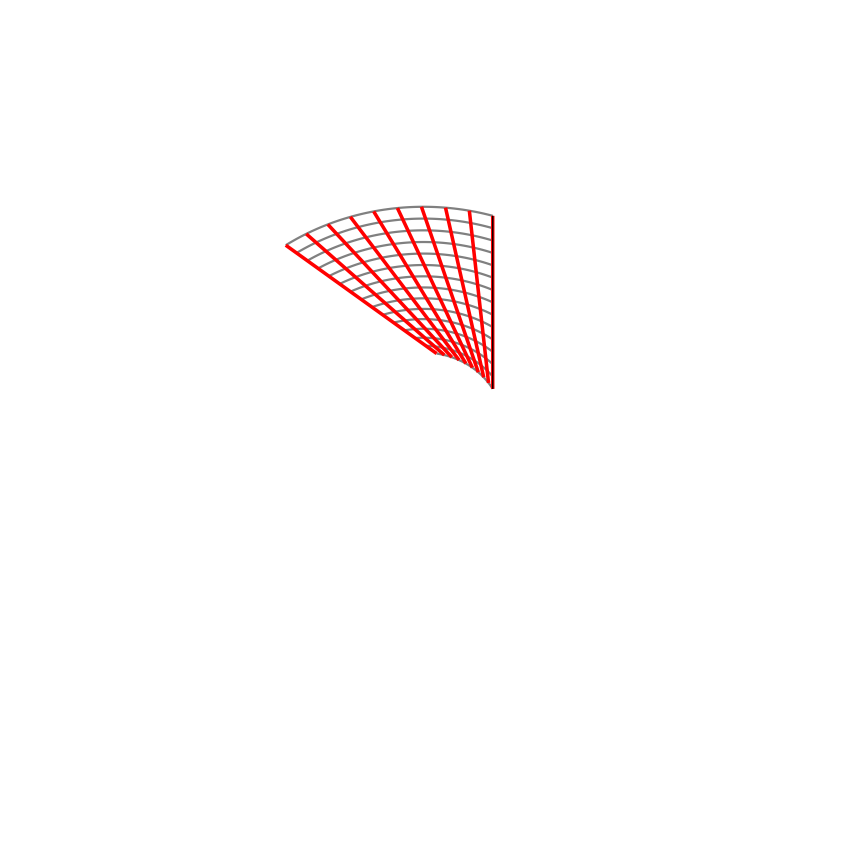

```mathematica
(* Initial Data *)
f =Log[x^2+y^2]+Log[(x-1)^2+y^2];
U={D[f,x],D[f,y]};
U=.4{-.5y,.4x};
γ={Cos[v],Sin[v]};
γ={2,v+1}

uCount=10;
uMin=0;
uMax=5;

v1=0;
v2=5;
vCount=15;

getSol[p0_,U_]:=Module[{Ut},
Ut=U/.{x->x[u],y->y[u]};
p={x[u],y[u]}/.NDSolve[{x'[u]==Ut[[1]],y'[u]==Ut[[2]],x[0]==p0[[1]],y[0]==p0[[2]]},{x,y},{u,0,10}];
p[[1]]
];

S[uVal_,ps_]:=Module[{},
{xs,ys}=Transpose[(ps/.u->uVal)];
vs=N[Table[v,{v,v1,v2,(v2-v1)/(vCount-1)}]];
xs = Interpolation[Transpose[{vs,xs}]];
ys = Interpolation[Transpose[{vs,ys}]];
np={xs[v],ys[v]}
];

ps=Table[getSol[γ,U],{v,v1,v2,(v2-v1)/(vCount-1)}];
fG=ParametricPlot[ps,{u,uMin,uMax},PlotRange->10,PlotStyle->Directive[Gray]];
γG=ParametricPlot[γ,{v,v1,v2},PlotStyle->Directive[Black,Thick]];


ss=Table[S[u,ps],{u,uMin,uMax,(uMax-uMin)/(uCount-1)}];
sG=ParametricPlot[ss,{v,v1,v2},PlotRange->10,PlotStyle->Directive[Red,Thickness[.003]]];

Show[fG,sG,γG,Axes->False]
```

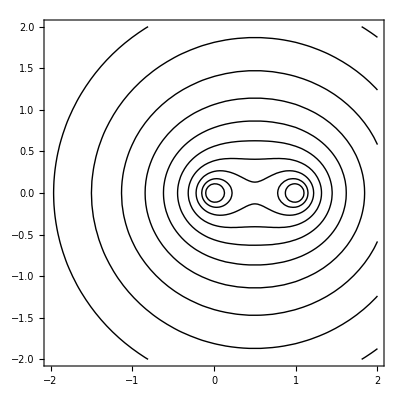

```mathematica
s=2;
ContourPlot[f,{x,-s,s},{y,-s,s},ContourShading->None, Contours->10]
```